# Bootstrapping v4.0 (smh)

## I mean at some point I am bound to get this right

```mathematica
ModuleDirectory = NotebookDirectory[] <> "../modules/";
<< (ModuleDirectory<> "debugTools.wl");
<< (ModuleDirectory<> "dataLoader.wl");
<< (ModuleDirectory<> "bootstraptdl.wl");
<< (ModuleDirectory<> "defect.wl");
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

```mathematica
?dataLoader`*
```

```mathematica
md = ModularDataFoldZ2FixedMinimal[] // Time;
mb = ModularBootstrapTraces[md] //Time;
traces = mb["defects"] // ToRoots//Time;
traces //Transpose // MatrixForm
```

Time:   0.068169

Time:   1.4693

Time:   0.229206

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | √5 | -√5 | -1 | 1 | 0 | 0 | 0 | -√(3-√5) | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | -√(5-√5) | √(5-√5) | √(5-√5) | 0 | 0 | 0 | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | -1+√5 | 1-√5 | 0 | 0 | 0 | √(3-√5) | -√(3-√5) | √(3-√5) | -√(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | √(7-3 √5) | -√(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | -1-√5 | 1+√5 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | -2 | 0 | 0 | 0 | 0 | -1 | -1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | -√5 | √5 | -1 | 1 | 0 | 0 | 0 | -√(3+√5) | -√(3-√5) | √(3-√5) | √(3+√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | -1+√5 | 1-√5 | 0 | 0 | 0 | -√(3-√5) | √(3-√5) | -√(3-√5) | √(3-√5) | 0 | 0 | 3-√5 | -3+√5 | 0 | -√(7-3 √5) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | -2+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6+2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | -√(5+√5) | √(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | √2 | -√2 | -√5 | √5 | -1 | 1 | 0 | 0 | 0 | √(3+√5) | √(3-√5) | -√(3-√5) | -√(3+√5) | 0 | 0 | -2 | 2 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | √(5-√5) | √(5-√5) | -√(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3+√5) | 1/2 (3-√5) | 1/2 (3-√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(2 (5-2 √5)) | √(2 (5-2 √5)) | √(2 (5-2 √5)) | -√(2 (5-2 √5)) | 0 | 0
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) |  |  | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | -√(7-3 √5) | -√(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) |  |  |  |  | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | 2 √(2 (5-2 √5)) | -2 √(2 (5-2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | -6-2 √5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | √5 | -√5 | -1 | 1 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) | -√(3-√5) | 0 | 0 | -2 | 2 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 0 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | √(5+√5) | √(5+√5) | -√(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | 0 | 0
1 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (-3-√5) | 1/2 (3+√5) | 1/2 (3+√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(2 (5+2 √5)) | -√(2 (5+2 √5)) | -√(2 (5+2 √5)) | √(2 (5+2 √5)) | 0 | 0
-2 | 0 | 2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | -1-√5 | 1+√5 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | 0 | 3+√5 | -3-√5 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
2 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | -1 | 1 | 1 | -1 | -√2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(2 (5-√5)) | -√(2 (5-√5)) | √(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) |  |  | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | -√(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | -√(2 (5-√5)) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) |  |  |  |  | 2 √(2 (5-2 √5)) | 2 √(2 (5-2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | -2 √(2 (5+2 √5))
1 | -1 | 1 | 1 | -1 | √2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5))
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(2 (5+2 √5)) | 2 √(2 (5+2 √5)))

```mathematica
d=md["S"][[1,1]]^(-2)//FullSimplify // Echo;
r=Total@Flatten[md["Z"]^2]  // Echo;
```

160 (3+√5)

84

```mathematica
potts=ModularDataMinimal[6,5, "D"];
s=potts["S"];
z =potts["Z"];
z//Flatten//Total//Echo;
```

12

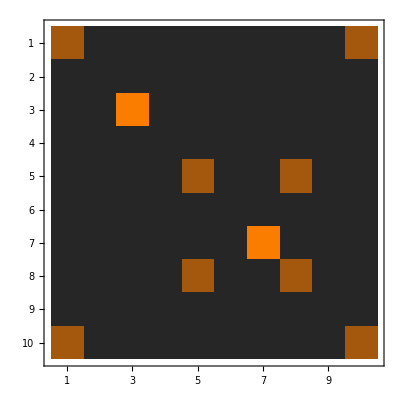

```mathematica
z//MatrixPlot
```

```mathematica
s//Simplify//MatrixForm
```

(1/2 √(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | 1/2 √(1/30 (5+√5)) | 1/2 √(1/10 (5+√5)) | √(1/30 (5-√5)) | 1/2 √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | 1/2 √(1/30 (5-√5))
1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | 0 | 1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5-√5)) | 0 | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5))
√(1/30 (5+√5)) | 0 | √(1/30 (5-√5)) | 0 | -√(1/30 (5-√5)) | 0 | -√(1/30 (5+√5)) | -√(1/30 (5-√5)) | 0 | √(1/30 (5+√5))
√(1/8-1/(8 √5)) | 1/2 √(1/10 (5+√5)) | 0 | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5)) | 0 | 1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5-√5))
1/2 √(1/30 (5+√5)) | √(1/8-1/(8 √5)) | -√(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | -1/2 √(1/30 (5-√5)) | √(1/8-1/(8 √5)) | √(1/30 (5+√5)) | -1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | 1/2 √(1/30 (5+√5))
1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5-√5)) | 0 | -1/2 √(1/10 (5+√5)) | √(1/8-1/(8 √5)) | √(1/8-1/(8 √5)) | 0 | -1/2 √(1/10 (5-√5)) | 1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5+√5))
√(1/30 (5-√5)) | 0 | -√(1/30 (5+√5)) | 0 | √(1/30 (5+√5)) | 0 | -√(1/30 (5-√5)) | √(1/30 (5+√5)) | 0 | √(1/30 (5-√5))
1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | -√(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | -1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5-√5)) | √(1/30 (5+√5)) | -1/2 √(1/30 (5-√5)) | 1/2 √(1/10 (5+√5)) | 1/2 √(1/30 (5+√5))
√(1/8-1/(8 √5)) | -1/2 √(1/10 (5+√5)) | 0 | √(1/8-1/(8 √5)) | -1/2 √(1/10 (5+√5)) | 1/2 √(1/10 (5+√5)) | 0 | 1/2 √(1/10 (5+√5)) | -1/2 √(1/10 (5-√5)) | -1/2 √(1/10 (5-√5))
1/2 √(1/30 (5-√5)) | -1/2 √(1/10 (5+√5)) | √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | 1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5+√5)) | √(1/30 (5-√5)) | 1/2 √(1/30 (5+√5)) | -1/2 √(1/10 (5-√5)) | 1/2 √(1/30 (5-√5)))

```mathematica
mb= ModularBootstrapTraces[md];
t=mb["defects"];
qdim = Transpose[t][[1]]//ToRoots;
nn=Length@qdim;
b=Array[Floor@N[qdim[[#1]]qdim[[#2]]/qdim[[#3]]] &, {nn,nn,nn}];
```

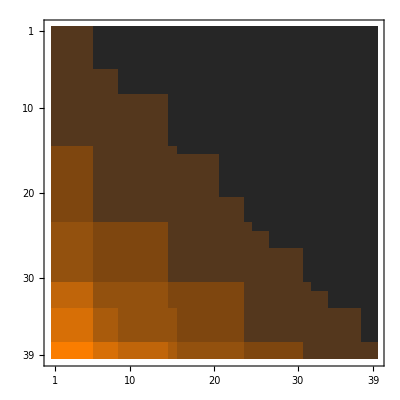
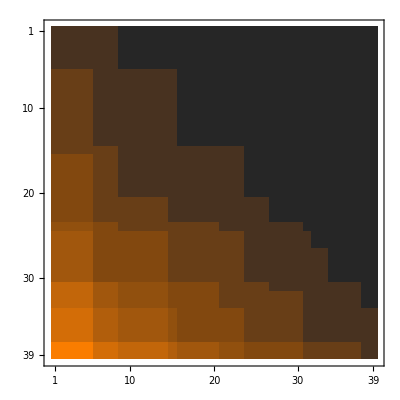
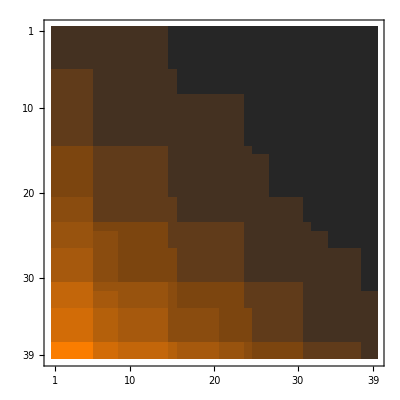
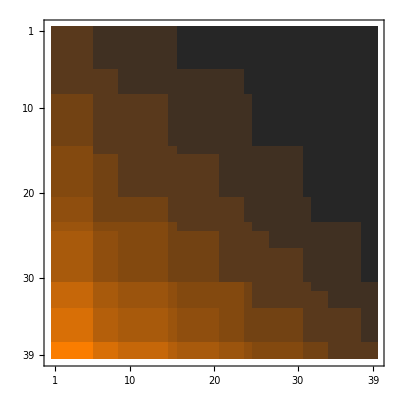
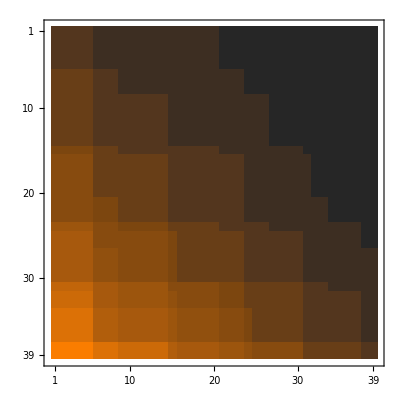
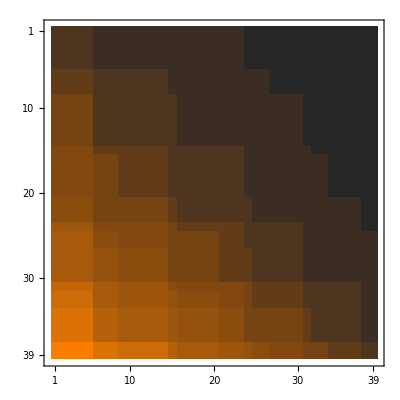
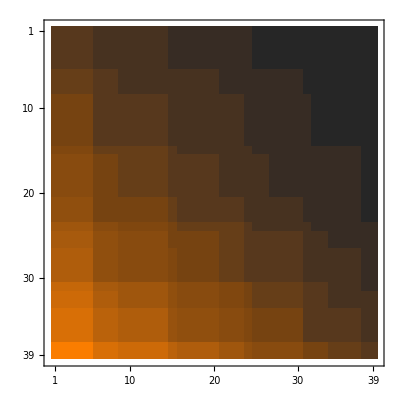
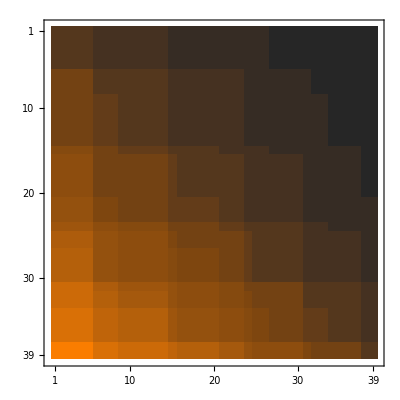
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot /@b
```

```mathematica
n=Array[x,{nn,nn,nn}];
```

```mathematica
Table[Sum[n[[i, j,k]]t[[k]],{k,1,nn}]-t[[i]]t[[j]],{i,1,nn},{j,1,nn}]
```